```mathematica
k1=0.3;k2=0.4;
```

```mathematica
f[p_]:=If[p<=k1,1,If[p>=k2,0,(k2-p)/(k2-k1)]]
```

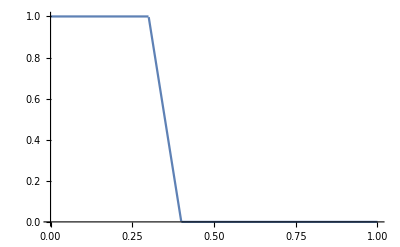

```mathematica
Plot[f[p],{p,0,1}]
```